This notebook shows another use of the XPS analysis functions, namely how to quickly find the distance between carbon and oxygen peaks.

### General i/o

```mathematica
<<"C:\\Users\\LukinLab\\My Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m";
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

Location of XPS excel file.

```mathematica
XPSPath="C:\\Users\\LukinLab\\My Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

List of samples

```mathematica
SampleList={00114,00113,00118,00117,00116,00115,10079,00119,10077,00019,10048};
```

Label by good/bad/other

```mathematica
StyleList={Red,Red,Blue,Blue,Red,Green,Green,Blue,Green,Blue,Green};
```

#### C Peak Setup

Use the GetSpec command to import the spectra from an excel file, keeping only the sheets containing the string specified in the third argument.

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,8];
```

I have already picked some values. They can be manipulated further by the PickGuesses command.

```mathematica
Ccoordlist={{{285,1000},{282.22999999999996,2600.},{289.59999999999997,2750.},{289.38,3250.}},{{285,1000},{282.71999999999997,2300.},{290.22999999999996,3900.},{283.03999999999996,2700.}},{{285,1000},{282.93,3000.},{290.08,2650.},{289.76,3200.}},{{285,1000},{283.15,2850.},{290.43,2450.},{289.99,2750.}},{{285,1000},{282.12,2550.},{289.94,2600.},{289.53999999999996,3200.}},{{285,1000},{282.7,3250.},{289.84999999999997,3150.},{289.45,3250.}},{{285,1000},{282.7,2350.},{290.26,2550.},{283.06,2550.}},{{285,1000},{282.65999999999997,2450.},{290.47999999999996,2350.},{290.03,3000.}},{{285,1000},{283.2,2650.},{290.61,2450.},{290.26,3000.}},{{285,1000},{282.47999999999996,1750.},{290.08,2800.},{282.93,2450.}},{{285,1000},{283.11,3000.},{290.47999999999996,3200.},{290.12,4000.}}};
```

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

{,,,,,,,,,,}

```mathematica
CData=UserRemoveAve[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

#### O Peak Setup

```mathematica
RawOData=GetSpec[XPSPath,"Excel XPS","O1s"];
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

11 spectra in all.

Importing Sheet O1s Scan J

Importing Sheet O1s Scan I

Importing Sheet O1s Scan H

Importing Sheet O1s Scan G

Importing Sheet O1s Scan F

Importing Sheet O1s Scan E

Importing Sheet O1s Scan D

Importing Sheet O1s Scan C

Importing Sheet O1s Scan B

Importing Sheet O1s Scan A

Importing Sheet O1s Scan

Formatting XPS Spectra

```mathematica
OSheets=GetSheets[XPSPath,"O1s"]
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

```mathematica
Ocoordlist=CoordInit[RawOData,532.5,7,12000]
```

{{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}}}

```mathematica
Ocoordlist={{{532.5,12000},{529.,12000},{536.,12000},{535.2,11800.}},{{532.5,12000},{529.,12000},{536.,12000},{529.6600000000001,12200.}},{{532.5,12000},{529.,12000},{536.,12000},{530.1,12200.}},{{532.5,12000},{529.,12000},{536.,12000},{529.82,12100.}},{{532.5,12000},{529.,12000},{536.,12000},{529.6400000000001,11950.}},{{532.5,12000},{529.,12000},{536.,12000},{529.44,12000.}},{{532.5,12000},{529.,12000},{536.,12000},{529.8800000000001,12000.}},{{532.5,12000},{529.,12000},{536.,12000},{529.7,11800.}},{{532.5,12000},{529.,12000},{536.,12000},{529.7,11900.}},{{532.5,12000},{529.,12000},{536.,12000},{529.7,12000.}},{{532.5,12000},{529.,12000},{536.,12000},{529.8800000000001,12050.}}};
```

```mathematica
PickGuesses[RawOData,Ocoordlist]
```

{,,,,,,,,,,}

```mathematica
OData=UserRemoveAve[RawOData,Ocoordlist];
```

```mathematica
CenteredOData=CenterAndNormalize/@OData;
```

### Carbon-Oxygen peak distance

#### Carbon data

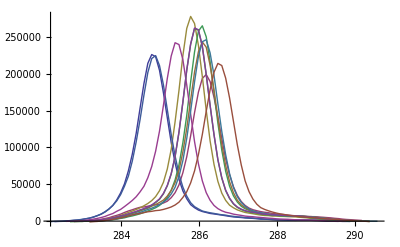

```mathematica
ListLinePlot[CData,PlotRange->All]
```

```mathematica
RawCFits=Model[#,1]&/@CData
```

{FittedModel[218822. ⅇ^(-2.88882 (-284.808+«12»)^2)],FittedModel[189247. ⅇ^(-2.71377 (-286.169+fitvar$28407)^2)],FittedModel[265972. ⅇ^(-3.44021 (-285.795+«12»)^2)],FittedModel[255232. ⅇ^(-3.37879 (-286.063+«12»)^2)],FittedModel[215520. ⅇ^(-2.83731 (-284.845+fitvar$28607)^2)],FittedModel[230486. ⅇ^(-2.89949 (-285.401+«12»)^2)],FittedModel[232583. ⅇ^(-3.04476 (-286.093+«12»)^2)],FittedModel[252525. ⅇ^(-3.3248 (-285.922+«12»)^2)],FittedModel[237294. ⅇ^(-3.07409 (-286.14+«12»)^2)],FittedModel[252844. ⅇ^(-3.29664 (-285.922+«12»)^2)],FittedModel[206020. ⅇ^(-2.69319 (-286.502+«12»)^2)]}

Sum of squares of residuals (as percent of total): 0.6691634705550638

Weight | μ | σ
1. | 284.808 | 0.41603

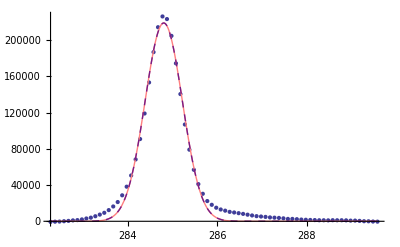

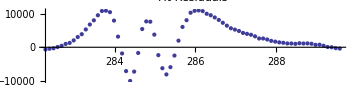

Sum of squares of residuals (as percent of total): 2.3364413295347837

Weight | μ | σ
1. | 286.169 | 0.429238

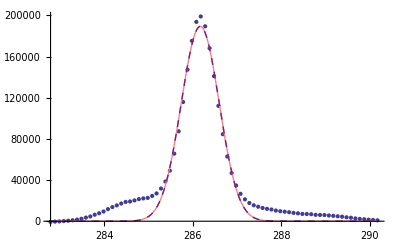

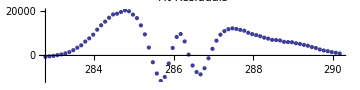

Sum of squares of residuals (as percent of total): 1.1436392798625339

Weight | μ | σ
1. | 285.795 | 0.381235

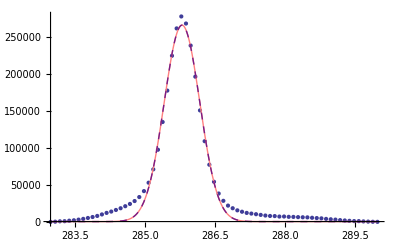

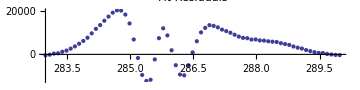

Sum of squares of residuals (as percent of total): 0.9885867465698895

Weight | μ | σ
1. | 286.063 | 0.384684

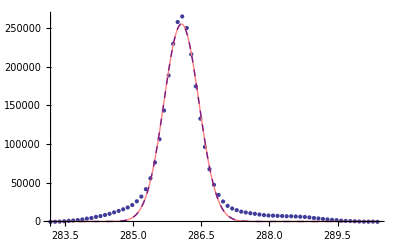

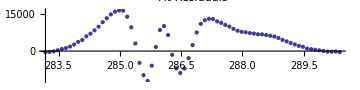

Sum of squares of residuals (as percent of total): 0.7907887962419643

Weight | μ | σ
1. | 284.845 | -0.41979

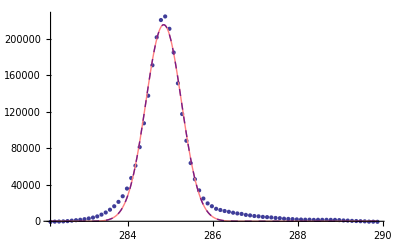

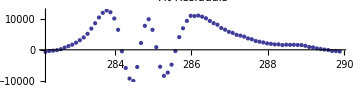

Sum of squares of residuals (as percent of total): 1.331240837612553

Weight | μ | σ
1. | 285.401 | 0.415264

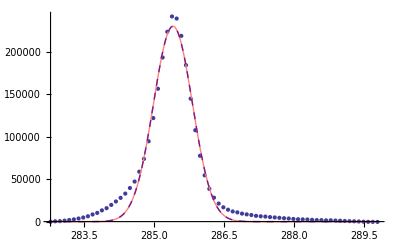

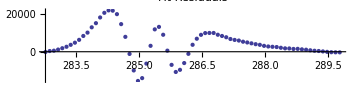

Sum of squares of residuals (as percent of total): 1.4149822436319777

Weight | μ | σ
1. | 286.093 | -0.405236

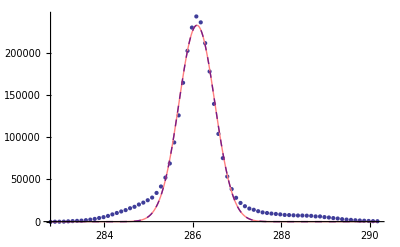

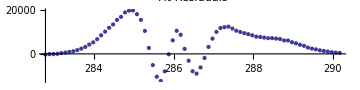

Sum of squares of residuals (as percent of total): 1.1197099763070315

Weight | μ | σ
1. | 285.922 | -0.387795

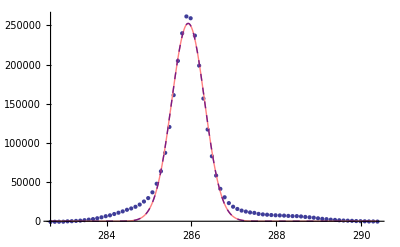

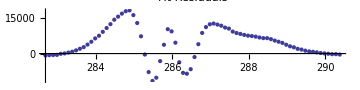

Sum of squares of residuals (as percent of total): 1.220849045687244

Weight | μ | σ
1. | 286.14 | -0.403298

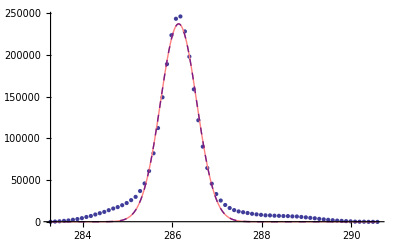

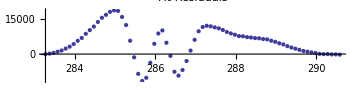

Sum of squares of residuals (as percent of total): 1.2118909040916428

Weight | μ | σ
1. | 285.922 | 0.389448

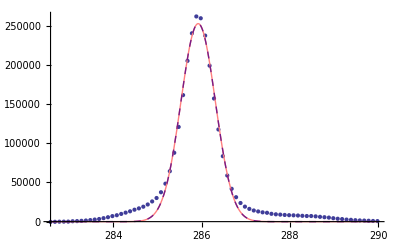

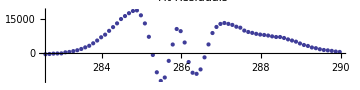

Sum of squares of residuals (as percent of total): 1.3091805074763663

Weight | μ | σ
1. | 286.502 | -0.430875

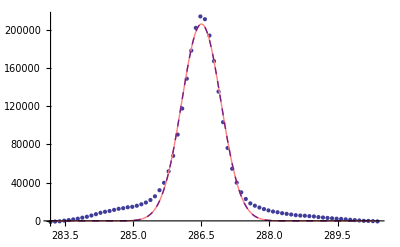

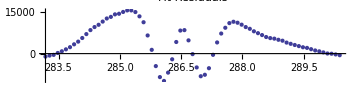

```mathematica
RawCSumms=Table[FitSummary[CData[[x]],RawCFits[[x]],"g"],{x,1,Length[RawCFits]}];
```

#### Oxygen data

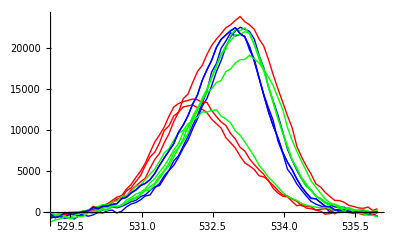

```mathematica
ListLinePlot[OData,PlotRange->All,PlotStyle->StyleList]
```

```mathematica
RawOFits=Model[#,{{5000,533,1}},"g",0.6,0.1]&/@OData;
```

```mathematica
RawOSumms=Table[FitSummary[OData[[x]],RawOFits[[x]],"g",False,False],{x,1,Length[RawOFits]}];
```

Sum of squares of residuals (as percent of total): 0.5487441525902212

Weight | μ | σ
1. | 532.166 | -0.866382

Sum of squares of residuals (as percent of total): 0.28651631271763034

Weight | μ | σ
1. | 532.928 | 0.979377

Sum of squares of residuals (as percent of total): 0.4745584852888966

Weight | μ | σ
1. | 532.931 | 0.738167

Sum of squares of residuals (as percent of total): 0.5752511969104098

Weight | μ | σ
1. | 533.033 | -0.777006

Sum of squares of residuals (as percent of total): 0.38082094285581003

Weight | μ | σ
1. | 532.181 | -0.890716

Sum of squares of residuals (as percent of total): 0.10736650041327281

Weight | μ | σ
1. | 532.41 | -0.898277

Sum of squares of residuals (as percent of total): 0.5887222179624376

Weight | μ | σ
1. | 532.984 | 0.819859

Sum of squares of residuals (as percent of total): 0.5996853746883567

Weight | μ | σ
1. | 532.837 | 0.825503

Sum of squares of residuals (as percent of total): 0.5014651787036721

Weight | μ | σ
1. | 532.994 | -0.815558

Sum of squares of residuals (as percent of total): 0.5996853746883567

Weight | μ | σ
1. | 532.837 | 0.825503

Sum of squares of residuals (as percent of total): 0.7394397895490638

Weight | μ | σ
1. | 533.031 | -0.951475

#### Differences

```mathematica
CPeakList=(Flatten/@RawCSumms)ᵀ[[2]]
```

{284.808,286.169,285.795,286.063,284.845,285.401,286.093,285.922,286.14,285.922,286.502}

```mathematica
OPeakList=(Flatten/@RawOSumms)ᵀ[[2]]
```

{532.166,532.928,532.931,533.033,532.181,532.41,532.984,532.837,532.994,532.837,533.031}

```mathematica
DiffList=OPeakList-CPeakList
```

{247.358,246.76,247.136,246.97,247.336,247.009,246.891,246.915,246.854,246.915,246.528}

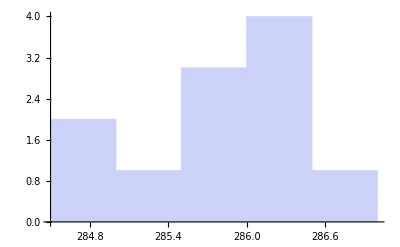

```mathematica
Histogram[CPeakList,"Wand"]
```

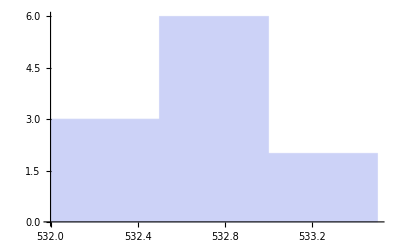

```mathematica
Histogram[OPeakList,"Wand"]
```

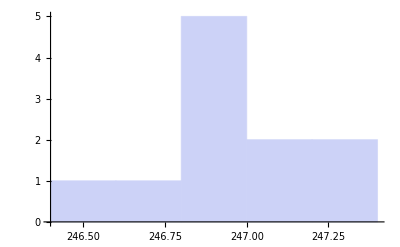

```mathematica
Histogram[DiffList,"Wand"]
```

Correcting the oxygen peak positions with the fitted carbon peak positions.

Here are the carbon peaks all on the same graph. They do in fact overlap.

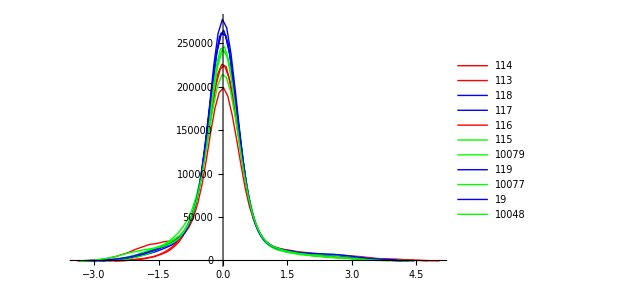

```mathematica
CorrectedCData=Table[{CData[[i]]ᵀ[[1]]-CPeakList[[i]],CData[[i]]ᵀ[[2]]}ᵀ,{i,1,Length[CData]}];
ListLinePlot[CorrectedCData,PlotRange->All,PlotStyle->StyleList,PlotLegends->SampleList]
```

Now, here are the oxygen peaks also all on the same graph, corrected by the carbon peak position.

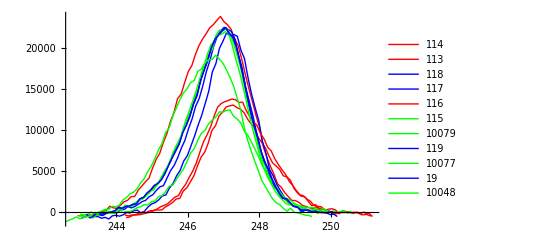

```mathematica
CorrectedOData=Table[{OData[[i]]ᵀ[[1]]-CPeakList[[i]],OData[[i]]ᵀ[[2]]}ᵀ,{i,1,Length[OData]}];
ListLinePlot[CorrectedOData,PlotRange->All,PlotStyle->StyleList,PlotLegends->SampleList]
```

#### Combine data

We can also simply splice the data together:

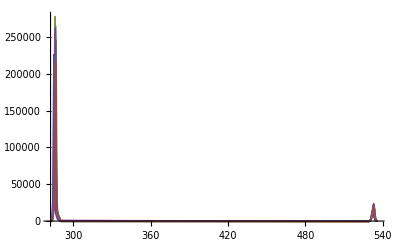

```mathematica
AllData=Table[Join[OData[[i]],CData[[i]]],{i,1,Length[OData]}];
ListLinePlot[AllData,PlotRange->All]
```

Center on the carbon peak and zoom in on the oxygen peak. This is just taking just the highest point in the carbon peak.

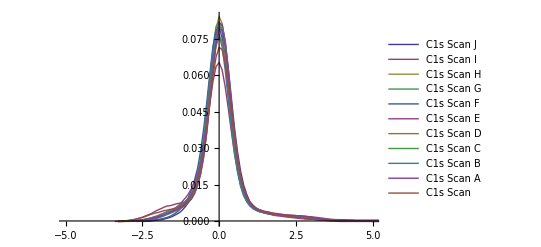

```mathematica
ListLinePlot[CenterAndNormalize[#]&/@AllData,PlotRange->{{-5,5},All},PlotLegends->CSheets]
```

Here is the resulting plot with the oxygen peak after the carbon peak position has been subtracted. It is virtually identical to the result above and is done with almost none of the same code.

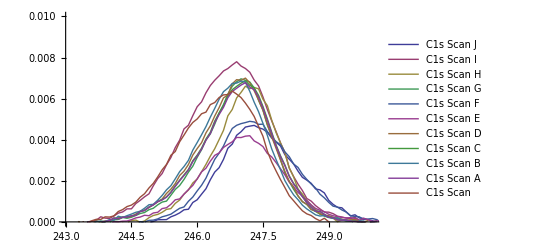

```mathematica
ListLinePlot[CenterAndNormalize[#]&/@AllData,PlotRange->{{243,250},{0,0.01}},PlotLegends->CSheets]
```